# Comparison of methods to obtain growth and growth rate from CAMB

Santiago Casas for the TeamFusion in the IST:L

Abstract

We test different ways of computing the growth and growth rate, using the Boltzmann code CAMB and a Mathematica wrapper, CosmoMathica.

The three methods include: directly obtaining δ(k,z) and dδ/da from CAMB, using the σ_8(z) and fσ_8(z) functions and finally using the ratio of power spectra P(k,z).

13/04/2020

## Fiducial Parameters

### Standard IST:F ΛCDM parameters

We use the same ΛCDM parameters as in the IST:F paper. The following set of parameters never change:

Ω_m=0.32

n_s=0.96

A_s=2.12605×10^-9

h=0.67

Ω_b=0.05

N_eff=3.046

## Cosmological Models

In this section we review the cosmological models used and show which parameters are changed at each step.

### Model 0: ΛCDM with massless neutrinos

w_0=-1

w_a=0

Total neutrino mass:

M_ν=0 eV

Number of massive neutrinos:

N_ν=0

Non-linear power spectrum method:

halofit=4 (Takahashi)

### Model 1: ΛCDM with massive neutrinos

w_0=-1

w_a=0

Total neutrino mass:

M_ν=0.06 eV

Number of massive neutrinos:

N_ν=1

Non-linear power spectrum method:

halofit=4 (Takahashi)

### Model 2: w_0 w_a CDM

w_0=-0.9

w_a=0.05

Total neutrino mass:

M_ν=0 eV

Number of massive neutrinos:

N_ν=0

Non-linear power spectrum method:

halofit=5 (Mead)

### Model 3: Hu-Sawicki f(R)

In this case f_(R,0) represents the value of f_R today, where  f_R==ⅆf(R)/ⅆR.

f_(R,0)=10^-4

n=1

Total neutrino mass:

M_ν=0 eV

Number of massive neutrinos:

N_ν=0

Non-linear power spectrum method:

halofit=9 (Winther)

### Model 3: Modified Gravity μ-η parametrization

We use in this case the Planck parametrization, with E_11 and E_22 as free parameters and a ΛCDM background.

μ(z)=1+Ω_DE(z)E_11

η(z)=1+Ω_DE(z)E_22

E_11=0.1007

E_22=0.8293

Total neutrino mass:

M_ν=0 eV

Number of massive neutrinos:

N_ν=0

Non-linear power spectrum method:

halofit=4 (Takahashi)

## Cosmological Observables

### Power Spectrum

We can write the linear power spectrum  as

P(k,z)=(A_s(k/k_0))^(n_s-1)T^2(k,z)

modulo some normalization factors of the primordial power spectrum and the transfer functions.

If the growth of structure is scale-independent, the transfer function can be factorized in:

T(k,z)=T(k)D(z)

where D_□(z) is the growth factor defined through the time-dependent matter density perturbation, as we will see below.

Here we plot the linear power spectrum of these different models in comparison:

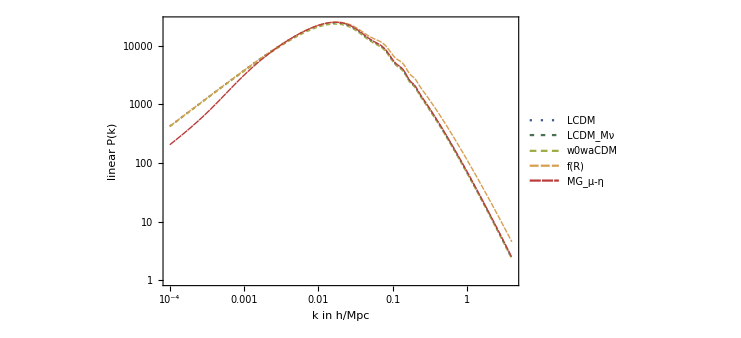

The non-linear power spectrum of these different models in comparison:

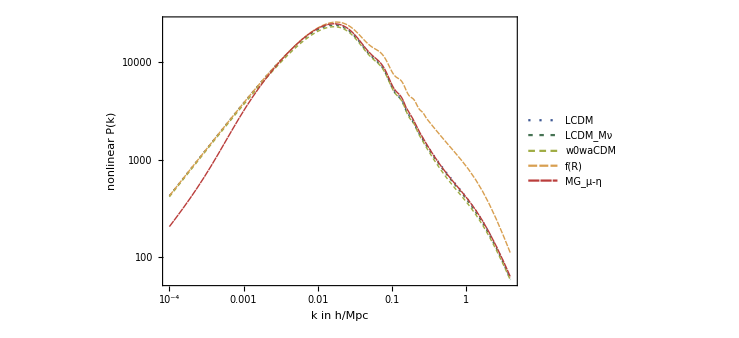

We can see that as expected, neutrinos tend to damp large scale structures at small scales, due to free streaming:

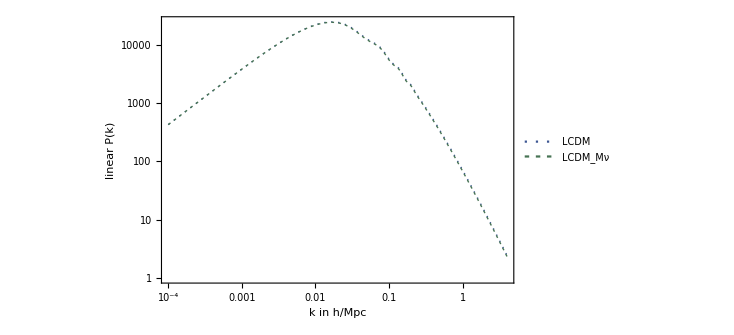

### Growth and Growth Rate from CAMB

We define the growth function D as

D(k,z)=δ_m(k,z)/δ_m(k,0)

In this general case, T(k,z)=δ(k,z)  and both are indistinguishable. In ΛCDM, where this is separable into a scale-dependent transfer function and a time-dependent growth function, one can usually find in the literature:

δ_m(k,z)=δ(k_i,z=0)T(k)D(z)

Where δ_m is the total matter density perturbation as calculated by the Boltzmann code CAMB, including CDM, baryons and neutrinos. This comes from a set of coupled time and scale dependent differential equations containing all matter species in an FLRW background.

The growth rate  f is defined as:

f(k,a)=ⅆln(δ_m)/ⅆln (a)

More specifically, this is implemented inside MGCAMB in this way:

equations_MG.f90
2531             ddelta= (ayprime(3)*grhoc+ayprime(4)*grhob)/(grhob+grhoc)
2532             delta=(grhoc*ay(3)+grhob*ay(4))/(grhob+grhoc)
2533             growthrate= ddelta/delta/adotoa

### Growth and Growth Rate from fσ_8

The code CAMB also calculates the “variance” of the density perturbation, measured in a spherical top-hat shell window function W_8(k) of size 8 Mpc/h. Inside CAMB, σ_8 is defined as:

(σ^2)_8(z) = ∫ⅆk/k W_8^2(k)(T^2)_δδ(k,z)𝒫_s(k)

where the primordial scalar power is 𝒫_s(k)=(A_s(k/k_0))^(n_s-1) and (T^2)_δδ(k,z)  is the transfer function of the total matter perturbation, δ_m.  One can also define the variance of the density-velocity perturbation, given by replacing T_δδ with T_δθ, where θ is the gradient of the velocity perturbation.

(σ^2)_(δθ, 8)(z) = ∫ⅆk/k W_8^2(k)(T^2)_δθ(k,z)𝒫_s(k)

In ΛCDM and in linear theory, the gradient of the velocity perturbation can  be approximated as

θ=δ_m f

Therefore, Eqn.(6) reduces in ΛCDM  to  (fσ_8(z))^2. One can then use these functions to define D_□(z)

D_s(z)=σ_8(z)/σ_8(0

and f(z) as

f_s(z)=(f σ_8)(z)/σ_8(z)

Since Eqns. (5-6) contain an integral over wavevectors k, this is only useful for scale-independent growth quantities. In the following, will identify this method with the subscript s.

### Growth and Growth Rate from ratios of Power Spectra

As we can see in Eqn.(1), the matter power spectra contains the transfer functions T^2(k,z), therefore we can directly obtain the growth factor D by taking ratios of linear power spectra:

D_p(k,z)=√(P_lin(k,z)/P_lin(k,z=0))

And since the growth rate is the logarithmic derivative of δ_m(k,z), we can obtain f by simply taking a derivative of that function:

f_p(k,z)=-ⅆln(D(k,z))/ⅆln (1+z)

In the following, will identify this method with the subscript p.

If one takes ratios of non-linear power spectra, a scale dependence in D(k,z) will appear, since at non-linear scales, the non-linear power spectrum doesn’t grow independently at each wavevector k, but rather the k-modes are coupled nonlinearly. We will call this growth function D_NL and we will show it below just for illustrative purposes.

D_NL(k,z)=√(P_NL(k,z)/P_NL(k,z=0))

### Growth factor from CAMB as a function of redshift

For the four models considered above, this is the growth factor extracted from CAMB as a function of redshift at k=0.1h/Mpc. One can see that f(R) is the model that differs the most from the others.

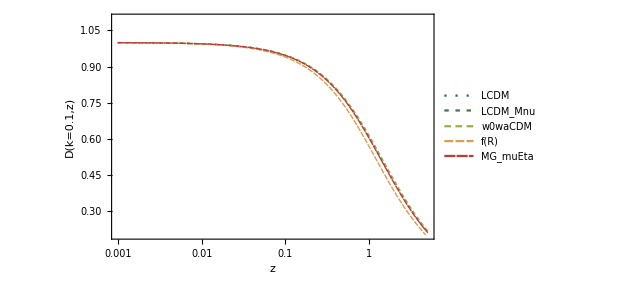

For the four models considered above, this is the growth factor extracted from CAMB as a function of redshift at  large scales, k=0.001h/Mpc. One can see that MG is the model that differs the most.

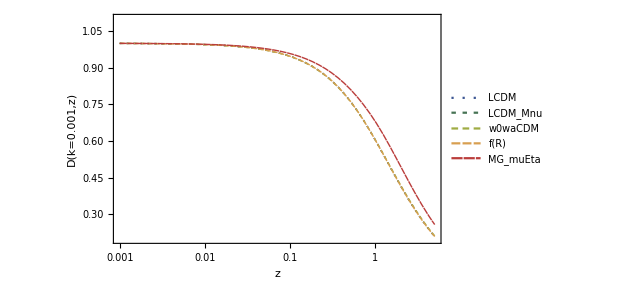

### Growth factor from CAMB as a function of scale

For the four models considered above, this is the growth factor extracted from CAMB as a function of scale k, at  z=1.0. One can see that f(R) is the model with the strongest scale-dependence. MG has a scale dependence at large scales and w0waCDM as a slight scale-dependence, at large scales, but it’s pretty much scale-independent.

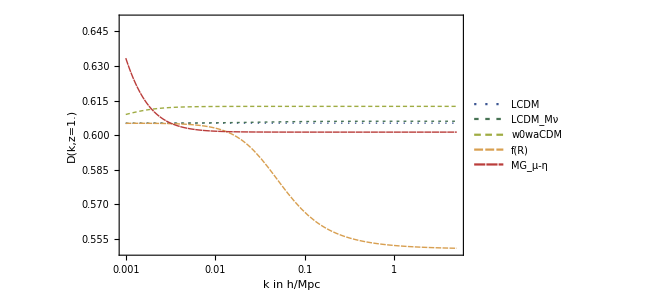

The Neutrino scale-dependence in the growth function can only be seen under a zoom-in into a smaller range, since the total neutrino mass is very small.

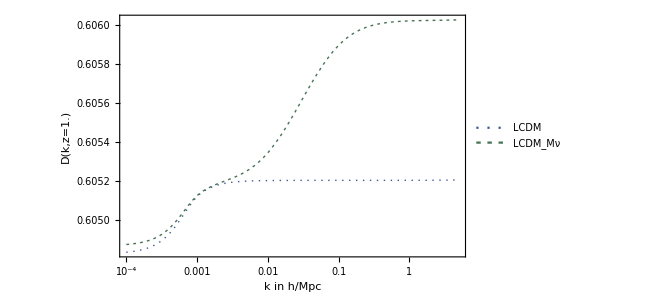

As one can see, there is also a slight scale-dependence even in the ΛCDM case at very large scales. These scales correspond to modes that entered the horizon before matter-radiation equality.

### Growth rate from CAMB as a function of redshift

For the four models considered above, this is the growth rate f(k,z) extracted from CAMB as a function of redshift at k=0.1h/Mpc. One can see that f(R) is the model that differs the most from the others.

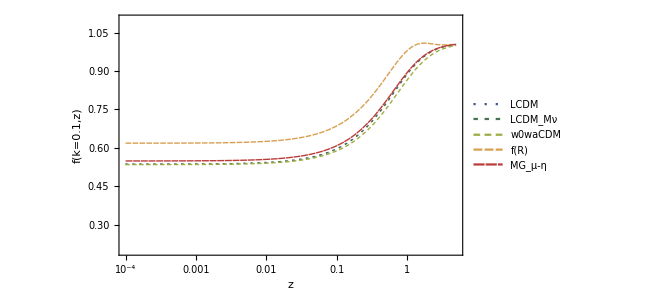

At much larger scales (k=0.0001h/Mpc) most models are very similar except the Modified Gravity model with μ and η.

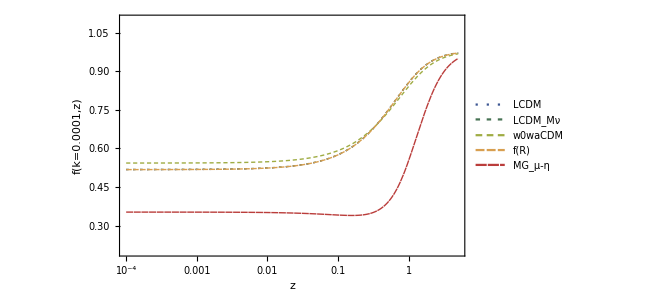

As a function of wavevector k, the growth rate looks like this at z=1.0:

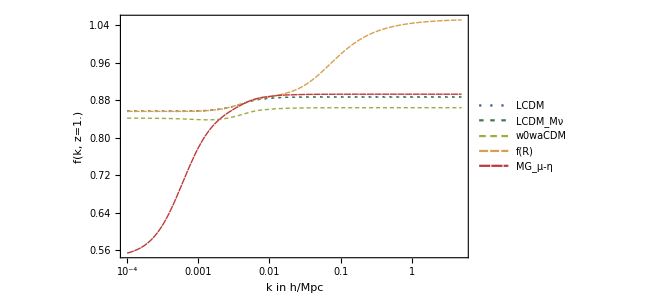

Again here, it is clearly visible that the MG and the f(R) models have the most scale-dependent behavior in f(k,z).  For ΛCDM, this function is very flat at k>0.01h/Mpc.

## Comparison of methods for the Growth D(k,z)

### ΛCDM with massless neutrinos (model 0)

For the growth function D(k,z), we now compare between the one computed from CAMB (Eqn. 3), named D, the one computed using σ_8 (Eqn. 9), named D_s and the one using the power spectra, D_p. We also show the non-linear growth D_NL, to remind the reader that the non-linear power spectrum exhibits mode coupling at non-linear scales (left: k=0.1 h/Mpc, right: k=0.5h/Mpc).

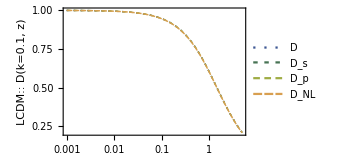
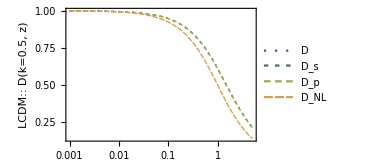

This is clearly seen as a function of scale for (z=1.0):

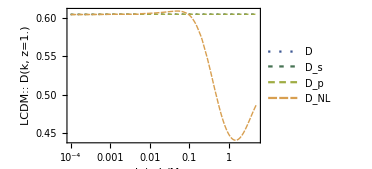

However for the actual linear quantity, the growth D(k,z) we don’t see a difference by eye. However, the ratio of quantities shows us some interesting differences. At large scales, we notice a difference in the order of 10^-3 for the D_s case. At small scales the differences are basically insignificant and come most probably from the interpolating functions.

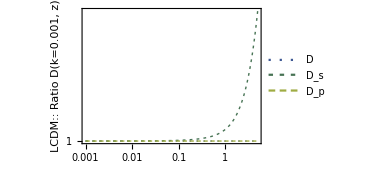
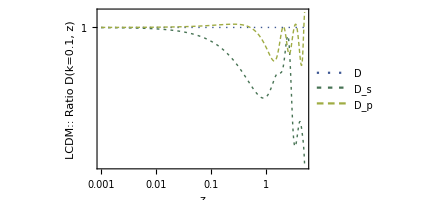

As a function of scale, we see that the method using σ_8 yields worst results at large scales. The best explanation for this is that the integral of Eqns. 6 and 7, is performed at small scales and doesn’t take into account the slight scale-dependence that exists at large scales.

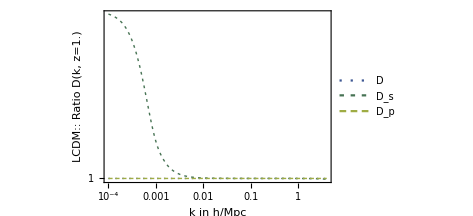

### ΛCDM with massive neutrinos and w0waCDM (model 1 and model 2)

Now we compare these three methods for other models a function of scale. The larger the scale dependence, especially at large scales, the more the discrepancy with the method using σ_8.

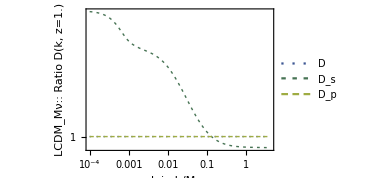
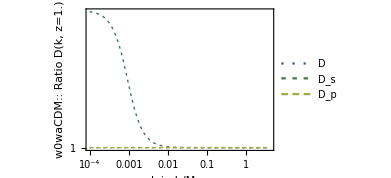

### f(R) and MG with μ,η (model 3 and model 4)

Now we compare these three methods for other models a function of scale. The larger the scale dependence, especially at large scales, the more the discrepancy with the method using σ_8. This is obvious, since the D_s method is by definition scale-independent.

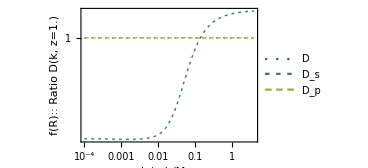
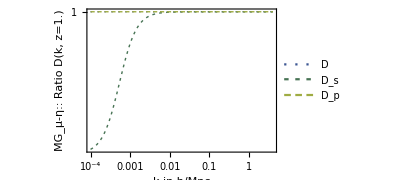

## Comparison of methods for the Growth Rate f(k,z)

### ΛCDM with massless neutrinos (model 0)

For the ΛCDM case with massless neutrinos we notice some differences in the three possible methods for the growth rate f(k,z). This comes from the fact that CAMB returns the derivative and not the logarithmic derivative of δ_m, so we need to normalize this derivative dividing by f(k,z)  at a high redshift, so that we recover f≈1  at a high z during matter domination. In the left plot we can see the evolution in redshift at a scale k=0.01, while in the right plot, its evolution as function of scale at z=1.

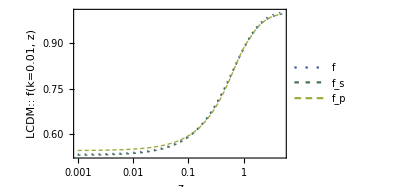
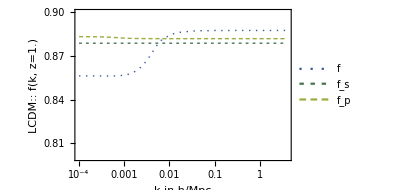

### Plotting the ratio to the baseline D(k,z) for model 0

If we plot the ratio of the f_p and f_s quantities to f (the one computed inside CAMB), we see that there are some differences in the redshift evolution. For f_s  there seems to be a normalization offset of about 1%, while for f_p there is some spurious redshift evolution with wiggles, possibly coming from an interpolating function, which for P_m(k,z) was chosen to be a spline of order three. As a function of scale (right panel) we see some scale dependence in the ratio at about 3% error.

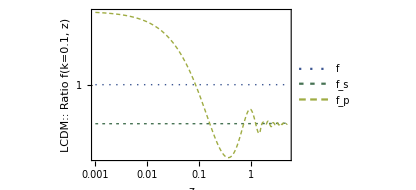
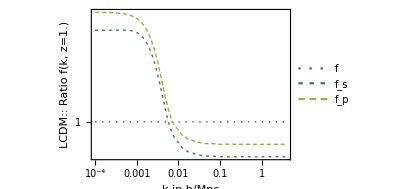

### ΛCDM with massive neutrinos and w0waCDM (model 1 and model 2)

As a function of redshift for a scale k=0.01 h/Mpc:

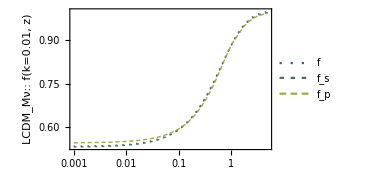
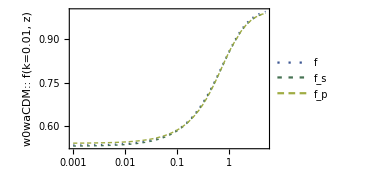

As a function of scale, for a redshift z=1.0:

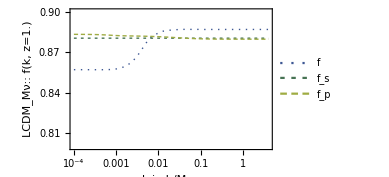
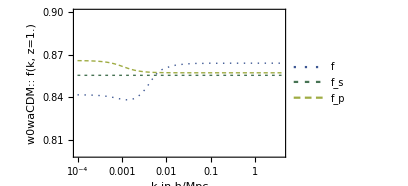

### f(R) and MG with μ,η (model 3 and model 4)

As a function of redshift for a scale k=0.01 h/Mpc:

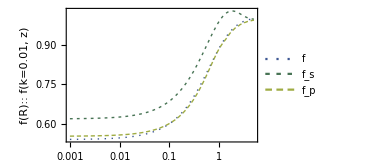
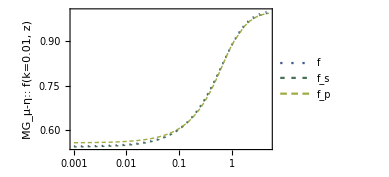

We see that the f_s  method, since it is not scale-dependent, yields really erroneous results for a scale dependent model.

As a function of scale, for a redshift z=1.0:

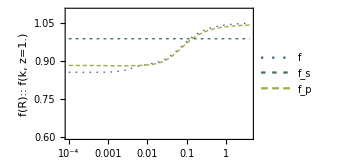
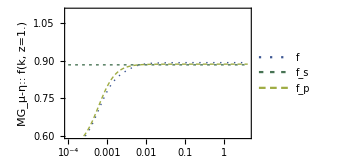

We see here that the method f_p is not capturing well the scale-dependence at large scales.

### Plotting the ratio to the baseline f(k,z) for f(R) and MG with μ,η (model 3 and model 4)

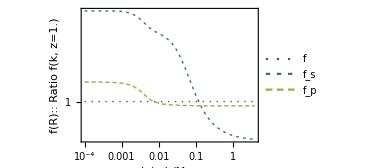
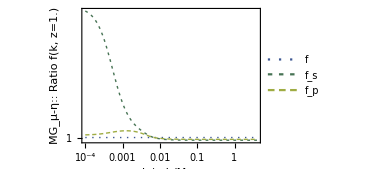

We see here that the method f_p is not capturing well the scale-dependence at large scales, since the ratio to the baseline f differs at k<0.01 at a few percent. The method f_s, of course, cannot capture the scale-dependence at all.

## Conclusions

We have investigated 5 models, ΛCDM with massless and massive neutrinos, w_0 w_aCDM, f(R) and Modified Gravity (MG) with a μ,η  parametrization. The model with neutrinos exhibits some scale dependence in the growth due to the erasure of structure by free streaming of neutrinos, f(R) has a strong scale-dependence due to a fifth force at small scales and MG has a scale dependence at large scales.

We have shown three methods to extract the observables, the growth rate f(k,z) and the growth D(k,z) using CAMB. The baseline one uses directly δ_m and its derivative computed inside CAMB. The method with a subscript “s”, is based on using σ_8 and fσ_8  as in  equations 6 and 7.  And finally the method with a subscript “p” is based on taking ratios of the power spectra as in equation 11.

For ΛCDM with massless neutrinos, the method “p” and “s” work fine for D(k,z) with very small errors at a subpermille level. However it is important to note that the method “p” can only be used, as intended, with linear power spectra. For f(k,z) there are some discrepancies at the percent level, probably coming from interpolating functions and a normalization of f(k,z) that depends on the highest available redshift z, extracted from CAMB.

For theories with scale dependence, such as ΛCDM with massive neutrinos, f(R), MG (and even w_0 w_aCDM at large scales, with high values of w_0), the method “s” does not work, since σ_8 it is per definition a scale-independent quantity. The method “p” works very well for D(k,z) even with scale dependence, with almost unnoticeable errors. However, it seems that for scale-dependent models, the method f_p is not capturing well the scale-dependence at large scales, with errors of a few percent. This might come from a normalization problem and partly due to the interpolation.